Pressure within an Accelerating Container

```mathematica
Manipulate[
Module[{g,hL,r,h,y,z,depth,P},
g=9.81;hL=1;r=0.25;h=1.75;
y=pt[[1]];z=pt[[2]];

depth=If[#<0,0,#]&@(-ay/g*y+hL-z);
P=ρ*g*depth;

If[depth≤0,pt={y,-ay/g*y+hL}];

Column[{
Text@Style[Column[{
"drag the ball to see pressure change",
Row@{"depth of ball = ",NumberForm[depth,{2,1}]," m",Spacer@20,
"gage pressure = ",NumberForm[P/1000,{3,1}]," kPa"}
},Center],18],

Plot[-ay/g*x+hL,{x,-r,r},PlotStyle->None,Filling->0,FillingStyle->Opacity[Rescale[ρ,{-500,2000}],Hue@0.6],PlotRange->{{-0.2-r,0.7-r},{-0.01,h}},Axes->False,ImageSize->{500,380},AspectRatio->Full,
Epilog->{
Thick,Line[{{-r,h},{-r,0},{r,0},{r,h}}],
{If[ay>0,Arrow[{{1.1*r,h*#},{1.1*r+r/2*Rescale[Abs@ay,{0,10}],h*#}}]],If[ay<0,Arrow[{{-1.1*r,h*#},{-1.1*r-r/2*Rescale[Abs@ay,{0,10}],h*#}}]]}&/@Range[0.1,0.9,0.2],
{RGBColor[1,0.6,0],PointSize@0.055,Point@pt},
}]
},Center]
],
Grid@{{
Control[{{ay,0,Row@{"acceleration (m/",Superscript["s",2],")"}},-10,10,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{ρ,1000,Row@{"density of fluid (kg/",Superscript["m",3],")"}},10,2000,10,Appearance->"Labeled",ImageSize->Small}],
Control[{{pt,{-0.224,0.064}},{-0.224,0.064},{0.224,1.686},Locator,Appearance->None}]
}}
]
```

```mathematica
Manipulate[
Module[{s1,s2},
s1=Rescale[ρ,{-500,2000}];
s2=Rescale[ρ,{-500,3000}];

Grid@{{
Graphics[{{EdgeForm@Thick,Opacity[s1,Hue@0.6],Rectangle[]},{c,Disk[1.5*{#,#},#]&@0.05},Text[Style[N@s1,17],{0.5,1},{0,-1}]}],
Graphics[{{EdgeForm@Thick,Opacity[s2,Hue@0.6],Rectangle[]},{c,Disk[1.5*{#,#},#]&@0.05},Text[Style[N@s2,17],{0.5,1},{0,-1}]}]
}}
],
Control[{{c,Black,""},{Black,Green,RGBColor[0,0.8,0],Orange,RGBColor[1,0.3,0],RGBColor[1,0.55,0],RGBColor[1,0.6,0],Magenta,Red,RGBColor[1,0,0.15],RGBColor[0.9,0,0]},Setter}],
Control[{{ρ,1000,Row@{"density of fluid (kg/",Superscript["m",3],")"}},10,2000,10,Appearance->"Labeled"}]
]
```

```mathematica
RGBColor[1.,0,0.15]
```

```mathematica
{#,RGBColor[0,#,0]}&/@Range[0.5,1,0.1]
```

{{0.5,RGBColor[0, 0.5, 0]},{0.6,RGBColor[0, 0.6, 0]},{0.7,RGBColor[0, 0.7, 0]},{0.8,RGBColor[0, 0.8, 0]},{0.9,RGBColor[0, 0.9, 0]},{1.,RGBColor[0, 1., 0]}}

```mathematica
(*Graphics[{{EdgeForm@Thick,Opacity[s1,Hue@0.6],Disk[]},Disk[{0,0},0.08]}];*)
```

```mathematica
{#,RGBColor[1,#,0]}&/@Range[0.3,0.7,0.1]
```

{{0.3,RGBColor[1, 0.3, 0]},{0.4,RGBColor[1, 0.4, 0]},{0.5,RGBColor[1, 0.5, 0]},{0.6,RGBColor[1, 0.6000000000000001, 0]},{0.7,RGBColor[1, 0.7, 0]}}

```mathematica
{#,Blend[{Red,Orange},#]}&/@Range[0,1,0.1]
```

{{0.,RGBColor[1., 0., 0.]},{0.1,RGBColor[1., 0.05, 0.]},{0.2,RGBColor[1., 0.1, 0.]},{0.3,RGBColor[1., 0.15000000000000002, 0.]},{0.4,RGBColor[1., 0.2, 0.]},{0.5,RGBColor[1., 0.25, 0.]},{0.6,RGBColor[1., 0.30000000000000004, 0.]},{0.7,RGBColor[1., 0.35000000000000003, 0.]},{0.8,RGBColor[1., 0.4, 0.]},{0.9,RGBColor[1., 0.45, 0.]},{1.,RGBColor[1., 0.5, 0.]}}

```mathematica
Manipulate[
Module[{g,hL,r,h,pt,y,z,depth,P},
g=9.81;hL=1;r=0.25;h=1.75;

pt={-0.224,0.064};
y=pt[[1]];z=pt[[2]];

depth=If[#<0,0,#]&@(-ay/g*y+hL-z);
P=ρ*g*depth;

If[depth≤0,pt={y,-ay/g*y+hL}];

Plot[-ay/g*x+hL,{x,-r,r},PlotStyle->None,Filling->0,FillingStyle->Opacity[Rescale[ρ,{-500,2000}],Hue@0.6],PlotRange->{{-0.2-r,0.7-r},{-0.01,h}},Axes->False,ImageSize->{500,380},AspectRatio->Full,
Epilog->{
Thick,Line[{{-r,h},{-r,0},{r,0},{r,h}}],
{If[ay>0,Arrow[{{1.1*r,h*#},{1.1*r+r/2*Rescale[Abs@ay,{0,10}],h*#}}]],If[ay<0,Arrow[{{-1.1*r,h*#},{-1.1*r-r/2*Rescale[Abs@ay,{0,10}],h*#}}]]}&/@Range[0.1,0.9,0.2],
}]
],
Grid@{{
Control[{{ay,0,Row@{"acceleration (m/",Superscript["s",2],")"}},-10,10,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{ρ,1000,Row@{"density of fluid (kg/",Superscript["m",3],")"}},10,2000,10,Appearance->"Labeled",ImageSize->Small}](*,
Control[{{pt,{-0.224,0.064}},{-0.224,0.064},{0.224,1.686},Locator,Appearance->None}]*)
}}
]
```

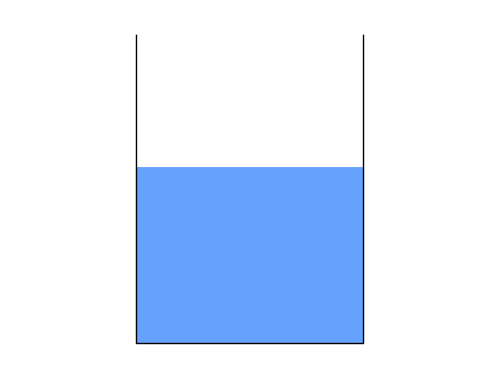
```mathematica
N@ImageAspectRatio@-Graphics-
```

0.76

This Demonstration shows how the pressure on a submerged ball varies with position, acceleration, and fluid density. Drag the black ball to change its position. Use sliders to set the fluid density and the acceleration of the tank in the y-direction. The intensity of the blue fluid in the tank changes with density.





The general equation of motion is used for both fluids at rest and in motion, where no shearing stress is present:

-∇P-γ k^⋀=ρ a  ,

where P is pressure, γ=ρg is specific weight, ρ is fluid density, g is acceleration due to gravity, and a is acceleration.

Using rectangular coordinates, this equation in component form is:

(∂P)/(∂x)=-ρ a_x,

(∂P)/(∂y)=-ρ a_y,

(∂P)/(∂z)=-(γ+ρ a_z) .

where z is depth

For a container of liquid accelerating in the y-direction at a constant rate, a_x and a_z drop out, and the change in pressure in terms of y and z is:

ⅆP=(∂P)/(∂y) ⅆy+(∂P)/(∂z) ⅆz,

ⅆP=-ρ a_y ⅆy-ρ g ⅆz.

Along a line of constant pressure ⅆP=0 so:

ⅆz/ⅆy=-a_y/g.

The depth of the ball z_2 is found by integrating the previous equation:

z_2=-a_y/g+z_1,

where z_1 is the depth of the ball when the tank is not accelerating.

The gage pressure at the location of the ball is the hydrostatic pressure:

P=ρ g z_2.

.

Reference

[1] W.W. Huebsch, B.R. Munson, T.H. Okiishi, and D.F. Young, Fundamentals of Fluid Mechanics, 6th ed., Hoboken: John Wiley & Sons, 2009.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

pressure

chemical engineering

rigid body motion

acceleration

fluids

fluid mechanics

Contributed by: Jon Barbieri and Peter Hassinger

Additional contributions by: Rachael L. Baumann

(University of Colorado Boulder, Department of Chemical and Biological Engineering)